```mathematica
Remove["Global`*"]
BCR[r_]=Piecewise[{{1, r^2≤1}, {0, True}}];
ConvolPair=FullSimplify[FunctionExpand[BCR[r]BCR[r-rp]]]
F[ρ_]=FourierTransform[BCR[r],{r},{ρ}]
FRT[ρ_]=F[ρ]F[ρ]
RT[r_]=FourierTransform[FRT[ρ],{ρ},{r}]
RT2[rp_]=Integrate[ConvolPair   ,{r,-1,1}]


(*AutoCor[r_]:=NIntegrate[BCR[r]BCR[r-rp],{rp,-1,1}]
plot=Table[AutoCor[r],{r,-1,1,.01}];
ListPlot[plot]*)
```

Piecewise[{{1, -1≤r≤1&&(r-rp)^2≤1}, {0, True}}]

(√(2/π) Sin[ρ])/ρ

(2 Sin[ρ]^2)/(π ρ^2)

(-2 Sign[-2+r]+r Sign[-2+r]-2 r Sign[r]+2 Sign[2+r]+r Sign[2+r])/(2 √(2 π))

Piecewise[{{2, rp==0}, {2-rp, 0<rp<2}, {2+rp, -2<rp<0}, {0, True}}]

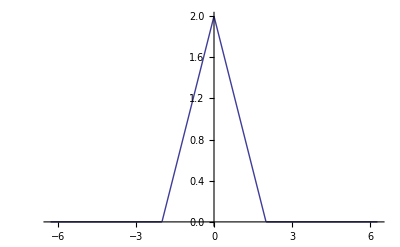

```mathematica
Plot[RT2[ρ],{ρ,-2π,2π}]
```

```mathematica
.
```